## Corrections to the Teukolsky equation

Here we show the correction to the Teukolsky potential, which takes the form δV(r)=(A_-2)/r^2+A_0+A_1 r+A_2 r^2
First we set the directory to where our folder “Potentials” is

```mathematica
SetDirectory[NotebookDirectory[]];
```

Then we define the angular numbers (l,m), type of correction (name= “even”, “odd”, “1”, “2”, “3”) and order of the spin expansion nmax. (Currently nmax=18 is available for l=2,3 and nmax=14 for l=4,5)

```mathematica
name="1";
nmax=18;
l=2;
m=2;
(*We get the file containing the correction to the potential*)
DumpGet["Potentials/deltaV-"<>ToString[name]<>"-a"<>ToString[nmax]<>"-s-2l"<>ToString[l]<>"m"<>ToString[Abs[m]]<>".mx"];
```

The correction of the potential is stored in the variables “deltaVminus” and “deltaVplus”, for each polarization type.
From these, we can read off the coefficients A_k

```mathematica
Am2=Series[Coefficient[deltaVminus,r,-2],{a,0,1}]
```

120 M w (2-ⅈ M w)+4/75 (900/M+(216 ⅈ)/(M^2 w)-16646 ⅈ w-9725 M w^2) a+O[a]^2

```mathematica
A0=Series[Coefficient[deltaVminus,r,0],{a,0,1}]
```

(2 (216+108 ⅈ M w-6446 M^2 w^2+1377 ⅈ M^3 w^3+3450 M^4 w^4))/(25 M^3 w)+((-90720 ⅈ+4476816 M w+7680558 ⅈ M^2 w^2-8841301 M^3 w^3-15007818 ⅈ M^4 w^4+1008000 M^5 w^5) a)/(7875 M^4 w)+O[a]^2

```mathematica
A1=Series[Coefficient[deltaVminus,r,1],{a,0,1}]
```

(2 (-2268+378 ⅈ M w+57108 M^2 w^2-50393 ⅈ M^3 w^3+4575 M^4 w^4))/(525 M^4 w)+((238140 ⅈ-15840846 M w-9904104 ⅈ M^2 w^2+7512131 M^3 w^3+18275579 ⅈ M^4 w^4+11451000 M^5 w^5) a)/(55125 M^5 w)+O[a]^2

```mathematica
A2=Series[Coefficient[deltaVminus,r,2],{a,0,1}]
```

-(4 (378 ⅈ-675 M w-9968 ⅈ M^2 w^2+10200 M^3 w^3))/(525 M^4)-(2 (39690+2715111 ⅈ M w-6751590 M^2 w^2-8562946 ⅈ M^3 w^3+3744750 M^4 w^4) a)/(55125 M^5)+O[a]^2

In the case of theories that break parity (“odd” and “3”), the full expression of the potential is actually given by dV=deltaVplus/P4value, and  dV=deltaVminus/P4value, where P4value is a constant that is also provided in the .mx files. For example:

```mathematica
name="odd";
DumpGet["Potentials/deltaV-"<>ToString[name]<>"-a"<>ToString[nmax]<>"-s-2l"<>ToString[l]<>"m"<>ToString[Abs[m]]<>".mx"];
```

```mathematica
Series[P4value,{a,0,1}]
```

1/2 √(1+4/(M^2 w^2))-(8 a)/(3 (M √(4+M^2 w^2)))+O[a]^2

```mathematica
deltaV=Series[deltaVplus/P4value,{a,0,1}]
```

1/(√(1+4/(M^2 w^2)))2 ((120 ⅈ M w (2 ⅈ+M w))/r^2+(4 r^2 (378 ⅈ-675 M w-9968 ⅈ M^2 w^2+10200 M^3 w^3))/(525 M^4)-(2 (216+108 ⅈ M w-6446 M^2 w^2+1377 ⅈ M^3 w^3+3450 M^4 w^4))/(25 M^3 w)-(2 r (-2268+378 ⅈ M w+57108 M^2 w^2-50393 ⅈ M^3 w^3+4575 M^4 w^4))/(525 M^4 w))+(1/(3 (4+M^2 w^2)^(3/2))32 M w^2 ((120 ⅈ M w (2 ⅈ+M w))/r^2+(4 r^2 (378 ⅈ-675 M w-9968 ⅈ M^2 w^2+10200 M^3 w^3))/(525 M^4)-(2 (216+108 ⅈ M w-6446 M^2 w^2+1377 ⅈ M^3 w^3+3450 M^4 w^4))/(25 M^3 w)-(2 r (-2268+378 ⅈ M w+57108 M^2 w^2-50393 ⅈ M^3 w^3+4575 M^4 w^4))/(525 M^4 w))+1/(√(1+4/(M^2 w^2)))2 ((4 (-900/M-(216 ⅈ)/(M^2 w)+16646 ⅈ w+9725 M w^2))/(75 r^2)+(2 r^2 (39690+2715111 ⅈ M w-6751590 M^2 w^2-8562946 ⅈ M^3 w^3+3744750 M^4 w^4))/(55125 M^5)+(90720 ⅈ-4476816 M w-7680558 ⅈ M^2 w^2+8841301 M^3 w^3+15007818 ⅈ M^4 w^4-1008000 M^5 w^5)/(7875 M^4 w)-(r (238140 ⅈ-15840846 M w-9904104 ⅈ M^2 w^2+7512131 M^3 w^3+18275579 ⅈ M^4 w^4+11451000 M^5 w^5))/(55125 M^5 w))) a+O[a]^2

## Corrections to the QNM frequencies

Here we plot the numerical results for the linear corrections in the QNM frequencies, δω, together with their fitting polynomials

```mathematica
SetDirectory[NotebookDirectory[]]; (*Set the directory to the folder that contains the folders "Fits" and "QNM_shifts"*)
```

Choose for which the theory and modes you want to see the results

```mathematica
name="even"; (*Type of higher-derivative correction. Cubic corrections: "even", "odd". Quartic corrections: "1", "2", "3"*)
l=2; (*Angular harmonic number*)
mrange=Range[-l,l]; (*Range for the magnetic number m*)
n=2;(*Overtone number, where n=1 is the fundamental mode*)
χmax=0.8; (*Maximum angular momentum to be plotted*)
```

Compile the full next subsection, which imports the data from the folders

### Compile this

```mathematica
order=If[name=="even"||name=="odd","cubic_","quartic_"];
tabmplus=Table[Import["QNM_shifts/"<>ToString[order]<>ToString[name]<>"_domega_plus_l"<>ToString[l]<>If[mm≥ 0,"_m"<>ToString[mm],"_mm"<>ToString[Abs[mm]]]<>"_n"<>ToString[n-1]<>".txt","Table"],{mm,mrange}];
tabmminus=Table[Import["QNM_shifts/"<>ToString[order]<>ToString[name]<>"_domega_minus_l"<>ToString[l]<>If[mm≥ 0,"_m"<>ToString[mm],"_mm"<>ToString[Abs[mm]]]<>"_n"<>ToString[n-1]<>".txt","Table"],{mm,mrange}];
fitplus=Table[Import["Fits/"<>ToString[order]<>ToString[name]<>"_plus_l"<>ToString[l]<>If[Abs[mm]≥ 0,"_m"<>ToString[Abs[mm]],"_mm"<>ToString[Abs[mm]]]<>"_n"<>ToString[n-1]<>".txt","Table"],{mm,mrange}];
fitminus=Table[Import["Fits/"<>ToString[order]<>ToString[name]<>"_minus_l"<>ToString[l]<>If[Abs[mm]≥ 0,"_m"<>ToString[Abs[mm]],"_mm"<>ToString[Abs[mm]]]<>"_n"<>ToString[n-1]<>".txt","Table"],{mm,mrange}];
fitReplus=Table[Sum[fitplus[[j]][[i,2]](Sign[mrange[[j]]+0.1]χ)^fitplus[[j]][[i,1]],{i,Length[fitplus[[j]]]}],{j,Length[mrange]}];
fitImplus=Table[Sum[fitplus[[j]][[i,3]](Sign[mrange[[j]]+0.1]χ)^fitplus[[j]][[i,1]],{i,Length[fitplus[[j]]]}],{j,Length[mrange]}];
fitReminus=Table[Sum[fitminus[[j]][[i,2]](Sign[mrange[[j]]+0.1]χ)^fitminus[[j]][[i,1]],{i,Length[fitminus[[j]]]}],{j,Length[mrange]}];
fitImminus=Table[Sum[fitminus[[j]][[i,3]](Sign[mrange[[j]]+0.1]χ)^fitminus[[j]][[i,1]],{i,Length[fitminus[[j]]]}],{j,Length[mrange]}];
tol=0.05; (*We remove the data points that have a relative error larger than this value*)
imaxlistReplus=Table[Do[ival=Length[tabmplus[[j]]];If[Abs[tabmplus[[j,imax,4]]]/Max[Abs[tabmplus[[j,Range[1,imax],2]]]]>tol,ival=imax;Break[]];,{imax,2,Length[tabmplus[[j]]]}];
ival,{j,2l+1}];
imaxlistImplus=Table[Do[ival=Length[tabmplus[[j]]];If[Abs[tabmplus[[j,imax,5]]]/(Max[Abs[tabmplus[[j,Range[1,imax],3]]]])>tol,ival=imax;Break[]];,{imax,2,Length[tabmplus[[j]]]}];
ival,{j,2l+1}];
imaxlistReminus=Table[Do[ival=Length[tabmminus[[j]]];If[Abs[tabmminus[[j,imax,4]]]/(Max[Abs[tabmminus[[j,Range[1,imax],2]]]])>tol,ival=imax;Break[]];,{imax,2,Length[tabmminus[[j]]]}];
ival,{j,2l+1}];
imaxlistImminus=Table[Do[ival=Length[tabmminus[[j]]];If[Abs[tabmminus[[j,imax,5]]]/(Max[Abs[tabmminus[[j,Range[1,imax],3]]]])>tol,ival=imax;Break[]];,{imax,2,Length[tabmminus[[j]]]}];
ival,{j,2l+1}];
```

### Plots

Real part of δω, + polarization

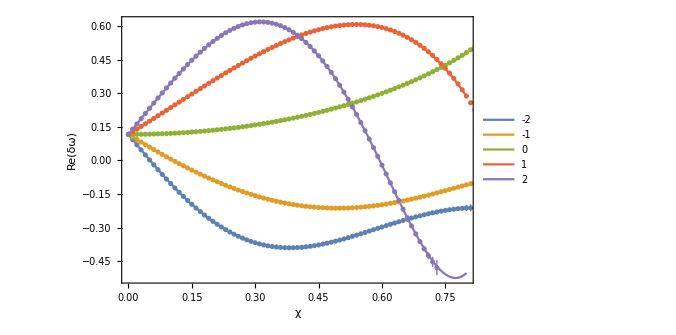

```mathematica
plotReplus=Show[Plot[Evaluate[Table[fitReplus[[j]],{j,Length[mrange]}]],{χ,0,χmax},Frame->True,PlotRange->Full,FrameLabel->{Style["χ",20],Style["Re(δω)",20]},PlotLegends->mrange ,AspectRatio->0.67,ImageSize->500,BaseStyle->{FontSize-> 13}],ListPlot[Table[Table[{tabmplus[[j,i,1]],Around[tabmplus[[j,i,2]],Abs[tabmplus[[j,i,4]]]]},{i,1,imaxlistReplus[[j]]}],{j,2l+1}],PlotRange->All,Frame->True,PlotLegends->None ,AspectRatio->0.67,ImageSize->500]]
```

Imaginary part of δω, + polarization

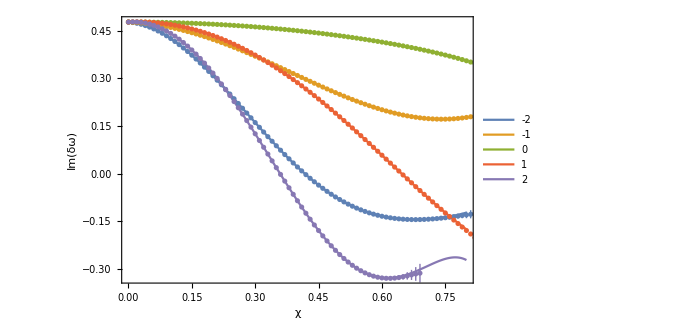

```mathematica
plotImplus=Show[Plot[Evaluate[Table[fitImplus[[j]],{j,Length[mrange]}]],{χ,0,χmax},Frame->True,PlotRange->Full,FrameLabel->{Style["χ",20],Style["Im(δω)",20]},PlotLegends->mrange,AspectRatio->0.67,ImageSize->500,BaseStyle->{FontSize-> 13}],ListPlot[Table[Table[{tabmplus[[j,i,1]],Around[tabmplus[[j,i,3]],Abs[tabmplus[[j,i,5]]]]},{i,1,imaxlistImplus[[j]]}],{j,2l+1}],PlotRange->All,Frame->True,PlotLegends->None ,AspectRatio->0.67,ImageSize->500]]
```

Real part of δω, - polarization

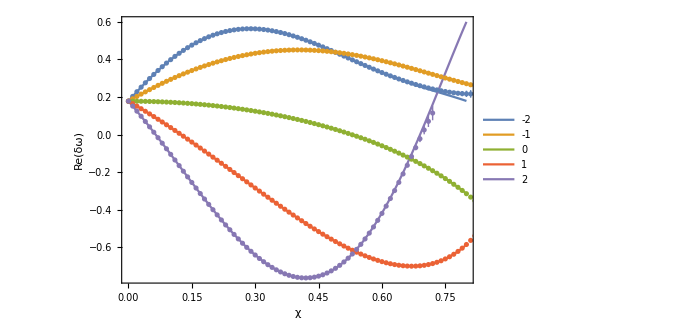

```mathematica
plotReminus=Show[Plot[Evaluate[Table[fitReminus[[j]],{j,Length[mrange]}]],{χ,0,χmax},Frame->True,PlotRange->Full,FrameLabel->{Style["χ",20],Style["Re(δω)",20]},PlotLegends->mrange ,AspectRatio->0.67,ImageSize->500,BaseStyle->{FontSize-> 13}],ListPlot[Table[Table[{tabmminus[[j,i,1]],Around[tabmminus[[j,i,2]],Abs[tabmminus[[j,i,4]]]]},{i,1,imaxlistReminus[[j]]}],{j,2l+1}],PlotRange->All,Frame->True,PlotLegends->None ,AspectRatio->0.67,ImageSize->500]]
```

Imaginary part of δω, - polarization

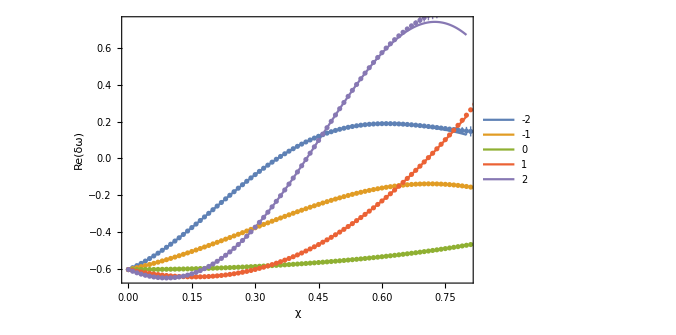

```mathematica
plotImminus=Show[Plot[Evaluate[Table[fitImminus[[j]],{j,Length[mrange]}]],{χ,0,χmax},Frame->True,PlotRange->Full,FrameLabel->{Style["χ",30],Style["Re(δω)",30]},PlotLegends->mrange ,AspectRatio->0.67,ImageSize->500,BaseStyle->{FontSize-> 13}],ListPlot[Table[Table[{tabmminus[[j,i,1]],Around[tabmminus[[j,i,3]],Abs[tabmminus[[j,i,5]]]]},{i,1,imaxlistImminus[[j]]}],{j,2l+1}],PlotRange->All,Frame->True,PlotLegends->None ,AspectRatio->0.67,ImageSize->500]]
```

Trajectory of δω in the complex plane, + polarization

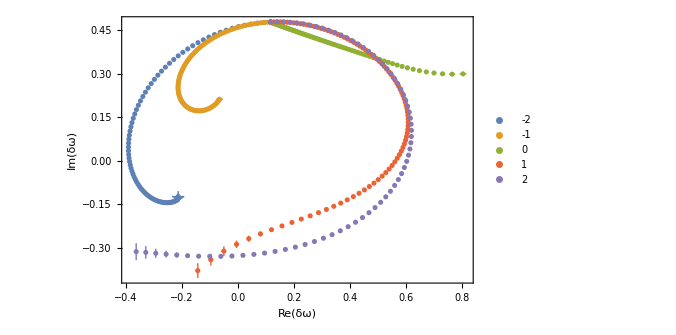

```mathematica
ListPlot[Table[Table[{Around[tabmplus[[j,i,2]],Abs[tabmplus[[j,i,4]]]],Around[tabmplus[[j,i,3]],Abs[tabmplus[[j,i,5]]]]},{i,Min[imaxlistImplus[[j]],imaxlistReplus[[j]]]}],{j,2l+1}],PlotRange->All,Frame->True,BaseStyle->{FontSize-> 13},FrameLabel->{Style["Re(δω)",20],Style["Im(δω)",20]},AspectRatio->0.67,ImageSize->500,PlotLegends->mrange]
```

Trajectory of δω in the complex plane, - polarization

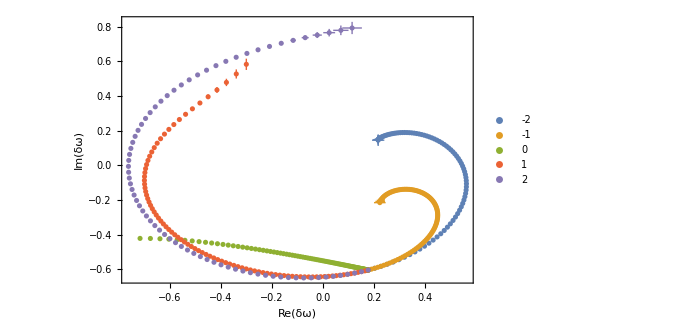

```mathematica
ListPlot[Table[Table[{Around[tabmminus[[j,i,2]],Abs[tabmminus[[j,i,4]]]],Around[tabmminus[[j,i,3]],Abs[tabmminus[[j,i,5]]]]},{i,Min[imaxlistImminus[[j]],imaxlistReminus[[j]]]}],{j,2l+1}],PlotRange->All,Frame->True,BaseStyle->{FontSize-> 13},FrameLabel->{Style["Re(δω)",20],Style["Im(δω)",20]},AspectRatio->0.67,ImageSize->500,PlotLegends->mrange]
```